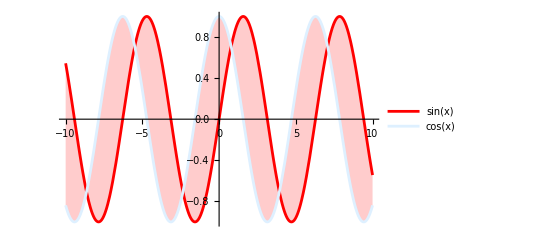

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotStyle->{Red,LightBlue},PlotLegends->"Expressions",Axes->{True,False}, Filling->{1->{2}}]
(*1-> {2} shows that color from function 1 to function 2*)
(*you can remove the axies with Axes argument in the sq bracket, for eg flase true, true false, false false, true true*)
```

```mathematica
var=Table[n!,{n,1,20}]
(*table command creates a 1D array.*)
```

{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

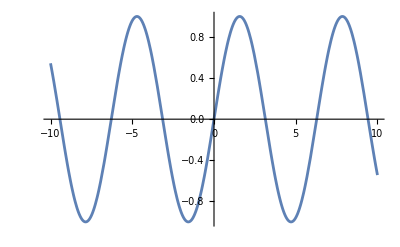
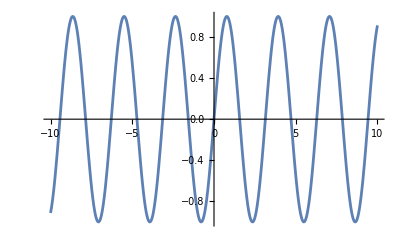
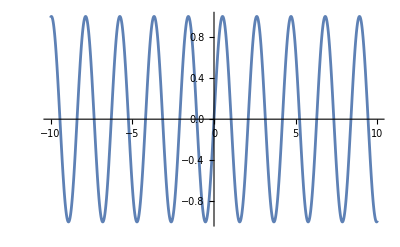
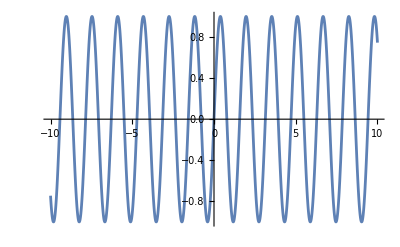

```mathematica
(*plotting a 1D array of sine*)
(*for multiplication, put a space or a an '*'*)
Table[Plot[{Sin[n x]},{x,-10,10}],{n,1,4}]
```

```mathematica
(*plotting a list*)
ListPlot[var,Joined->True,Mesh->All]
```

-Graphics-

{1,16,81,256,625,1296,2401,4096,6561,10000}

{4,16,64,256,1024,4096,16384,65536,262144,1048576}

{1,2,6,24,120,720,5040,40320,362880,3628800}

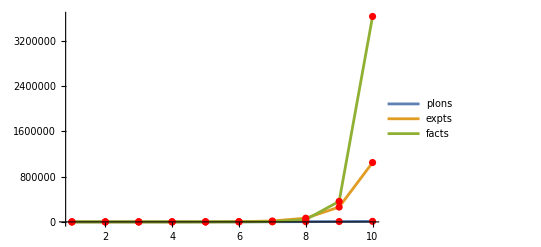

```mathematica
plyno=Table[n^4,{n,1,10}]
expt=Table[4^n,{n,1,10}]
facts=Table[n!,{n,1,10}]
ListPlot[{plyno,expt,facts},Joined->True,Mesh->All,MeshStyle->Red,PlotLegends->Placed[{"plons","expts","facts"}, Below],PlotRange->Full]
```

```mathematica
(*manipulate adds a slider*)
Manipulate[Plot[Sin[n x],{x,-10,10}],{n,1,10}]
```

```mathematica
func=4 x^3-12 x^2+1
```

1-12 x^2+4 x^3

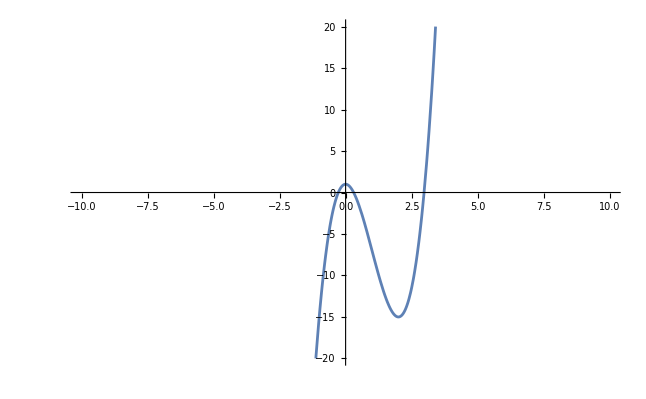

```mathematica
Plot[func,{x,-10,10},PlotRange->{-20,20}]
```

```mathematica
(*crude method to find the 0, last argument is the precision of the digits.*)
root=Table[{x,func},{x,0.303,0.305,0.0001}]
root
```

{{0.303,0.00956451},{0.3031,0.0089474},{0.3032,0.00833012},{0.3033,0.00771267},{0.3034,0.00709505},{0.3035,0.00647727},{0.3036,0.00585932},{0.3037,0.00524121},{0.3038,0.00462292},{0.3039,0.00400447},{0.304,0.00338586},{0.3041,0.00276707},{0.3042,0.00214812},{0.3043,0.001529},{0.3044,0.000909717},{0.3045,0.000290265},{0.3046,-0.000329355},{0.3047,-0.000949141},{0.3048,-0.00156909},{0.3049,-0.00218921},{0.305,-0.0028095}}

{{0.303,0.00956451},{0.3031,0.0089474},{0.3032,0.00833012},{0.3033,0.00771267},{0.3034,0.00709505},{0.3035,0.00647727},{0.3036,0.00585932},{0.3037,0.00524121},{0.3038,0.00462292},{0.3039,0.00400447},{0.304,0.00338586},{0.3041,0.00276707},{0.3042,0.00214812},{0.3043,0.001529},{0.3044,0.000909717},{0.3045,0.000290265},{0.3046,-0.000329355},{0.3047,-0.000949141},{0.3048,-0.00156909},{0.3049,-0.00218921},{0.305,-0.0028095}}

```mathematica
(*gives all the roots together*)
N[Solve[4 x^3-12 x^2+1==0,x]]
```

{{x→-0.276237},{x→0.304547},{x→2.97169}}

```mathematica
- the 2 most common methods of finding the roots are:
	1. Biscetion method or bracketing method:
		- depends on the changing the sign of functions near the roots,  the you simply keep making an educated guess about the roots, by halfing everytime and 		checking the sign the new f(x).
		
	2. Newton raphson method
	
- neither of these methods are directly used in the solve method.
```

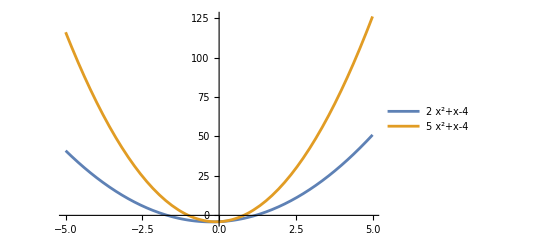

```mathematica
Plot[{2 x^2+x-4,5 x^2+x-4},{x,-5,5},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-5,5},PlotRange->{{-10,10},{-20,20}},Frame->True],{a,-5,5},{b,-5,5},{c,-10,10}]
```

## Week 2 (13-01-2025)

```mathematica
(*trajectory of minima*)
Manipulate[Plot[x^2+b x+A1,(-b/2^2+b ),{x,-5,5},PlotRange->{{-10,10},{-20,20}},Frame->True],{a,-5,5},{b,-5,5},{c,-10,10}]
```

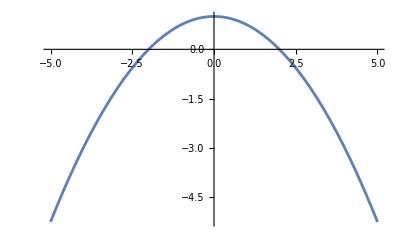

```mathematica
Plot[b^2/4-b^2/2+1,{b,-5,5}] (*this is the actual trajectory of minima*)
```

-Cos[x]

-1+x^2/2

1-1/2 (-π+x)^2

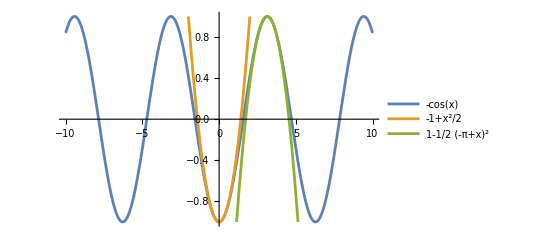

```mathematica
f1=-Cos[x]
f4=x^2/2-1 (*approximation of f1's minima at x=0*)
f5=1-(x-Pi)^2/2 (*approxiamtion of f2's first maxima*)
Plot[{f1,f4,f5},{x,-10,10},PlotLegends->"Expressions",PlotRange->{-1,1}]
```

```mathematica
f2=Sin[x]/x
f3=1/x^2-1/x
```

Sin[x]/x

1/x^2-1/x

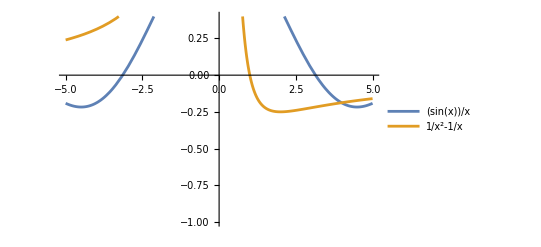

```mathematica
Plot[{f2,f3},{x,-5,5},PlotLegends->"Expressions",PlotRange->{-1,0.4}]
```

```mathematica
f2_series=Series[f2,{x,0,2}]
f3_series=Series[f3,{x,1.5,2}]
```

1-x^2/6+O[x]^3

-0.222222-0.148148 (x-1.5)+0.296296 (x-1.5)^2+O[x-1.5]^3

- functional forms such as k[1/x^m - 1/x^n] for m>n, we simply write the Taylor series at the minima.

```mathematica
func=-1/x +1/x^2
fun_se=Series[func,{x,2,2}]
(*ser*)(*=fun_se*)
```

1/x^2-1/x

-1/4+1/16 (x-2)^2+O[x-2]^3

fun_se

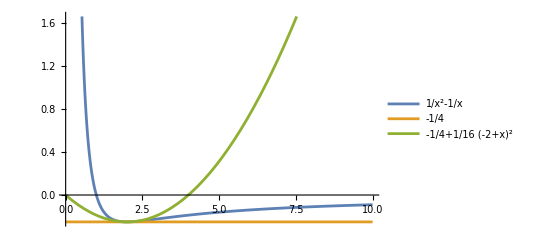

```mathematica
(*Plot[{func,ser},{x,0,5},PlotLegends->"Expressions"]*)
Plot[{func,Evaluate[Table[Normal[Series[func,{x,2,n}]],{n,2}]]},{x,0,10},PlotLegends->"Expressions"]
```

#### Radicals and logs. (14-1-25)

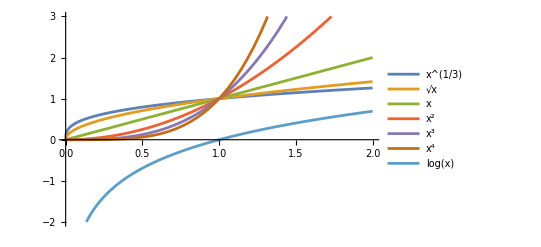

```mathematica
Plot[{x^(1/3),x^(1/2),x,x^2,x^3,x^4,Log[x]},{x,0,2},PlotRange->{-2,3},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{x^(1/n),Log[x]},{x,0,20},PlotRange->{0,10},PlotLegends->"Expressions"],{n,1,10}]
```

```mathematica
Manipulate[Plot[(x^(1/n)-Log[x]),{x,0,5}],{n,1,10}]
```

```mathematica
(* figuring out the exact value of n for which log x and x^1/n would be equal.*)
f=x^(1/n)
f2=Log[x]
(* how to equate 2 derivatives directly?*)
(*n0=e and x=e^e when we get exactly 1 intersection. we also infer that log is a slowly growing function.*)
(*do the same exrercise for r-x-e^-x, find r for which the function is 0*)
```

x^(1/n)

Log[x]

```mathematica
(*Define the functions*)
f1=x^(1/n);
f2=Log[x];

(*Take the derivatives*)
f1Prime=D[f1,x];
f2Prime=D[f2,x];

(*Use NSolve to find numerical solutions for n and x*)
NSolve[{f1==f2,f1Prime==f2Prime},{n,x}]
```

{{n→2.71828,x→15.1543}}

```mathematica
Manipulate[Plot[{r-x,Exp[-x]},{x,-5,5},PlotLegends->"Expressions",PlotRange->{-15,15}],{r,-5,5}]
```

```mathematica
(*doing the same routine for r-x-e^-x*)
(*Define the functions*)
func1=r-x;
func2=Exp[-x];

(*Take the derivatives*)
func1prime=D[func1,x];
func2prime=D[func2,x];

(*Use NSolve to solve the system of equations*)
NSolve[{func1==func2,func1prime==func2prime},{r,x}]
```

{{x→0.,r→1.},{x→0.-6.28319 ⅈ,r→1.-6.28319 ⅈ},{x→0.-12.5664 ⅈ,r→1.-12.5664 ⅈ},{x→0.-18.8496 ⅈ,r→1.-18.8496 ⅈ},{x→0.-25.1327 ⅈ,r→1.-25.1327 ⅈ},{x→0.-31.4159 ⅈ,r→1.-31.4159 ⅈ},{x→0.-37.6991 ⅈ,r→1.-37.6991 ⅈ},{x→0.-43.9823 ⅈ,r→1.-43.9823 ⅈ},{x→0.-50.2655 ⅈ,r→1.-50.2655 ⅈ},{x→0.-56.5487 ⅈ,r→1.-56.5487 ⅈ},{x→0.-62.8319 ⅈ,r→1.-62.8319 ⅈ},{x→0.-69.115 ⅈ,r→1.-69.115 ⅈ},{x→0.-75.3982 ⅈ,r→1.-75.3982 ⅈ},{x→0.-81.6814 ⅈ,r→1.-81.6814 ⅈ},{x→0.-87.9646 ⅈ,r→1.-87.9646 ⅈ},{x→0.-94.2478 ⅈ,r→1.-94.2478 ⅈ}}

#### Flow in 1 dimension.

ẋ=f(x), where f(x) is time independent “autonomous system”, 
- the points where f(x)=0, are called special points, called fixed points, these are the points where x won’t be changing with time, where if you reach, you’d  be trapped there and your position won’t be changing with time.
- we then check for the stability of those points

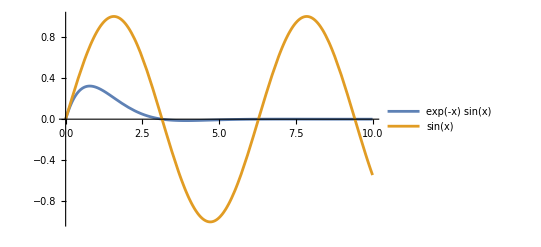

```mathematica
Plot[{Exp[-x] Sin[x],Sin[x]},{x,0,10},PlotRange->Full,PlotLegends->"Expressions"]
(*the curve is a degrading sin curve, so the stable fixed points would be same.*)
```

```mathematica
Manipulate[Plot[r+x^2,{x,-10,10},PlotRange->{-20,20}],{r,10,-10}]
```

```mathematica
(*for r=0, x=0 is a half stable fixed point, as it attracts some trajectories and repels some.*)
(*the system plotted above is a bifurcated system, as for some r, there are fixed points, but for others the fixed points don't exists.*)
```

```mathematica
Manipulate[Plot[1+r x+x^2,{x,-5,5},PlotRange->{-10,10}],{r,-5,5}]
```

#### Week 3 (20-1-25)

plot of x^{.} with x is called flow of of x.

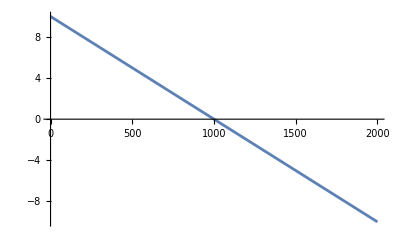

```mathematica
(*v0=10*)
Plot[10-x/100,{x,0,2000}](*
only 1 fixed point, and it is stable, it is the max charge the capacitor can handle.
*)
```

```mathematica
Manipulate[Plot[v/r-x/(r c),{x,0,3000},PlotRange->Full],{v,10,20},{r,1,5},{c,100,200}]
(*the value of maximum charge evidently is only dependent on v and c *)
```

## Population growth.

```mathematica
(*
N^{.}=rN, this would give a unrealistic model for population, cause it gives population to be infinite.
we rather use logistic equation to model the population.
N^{.}=rN(1-N/K), k is the carrying capacity, therefore N=K is the fixed point, the point where population tends to.
*)
```

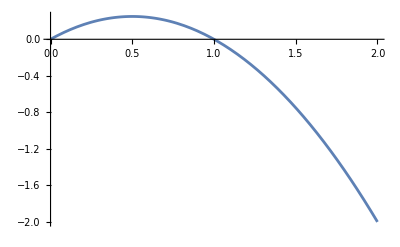

```mathematica
Plot[x (1-x),{x,0,2},PlotRange->Full]
```

```mathematica
Manipulate[Plot[r x (1- x/k),{x,0,10},PlotRange->{-5,5}],{r,1,3},{k,1,5}]
```

```mathematica
f1= a x (1-x)
```

a (1-x) x

```mathematica
Manipulate[Plot[f1/.a->a1,{x,0,10}],{a1,-5,5}]
(*
if you direclty use f1, it won't work, as manipulate will cause a problem, so you eihter use the replacemnet function i.e /.v->v1
*)
```

```mathematica
lorentzian= a^2/(x^2+a^2)
gaussian= Exp[-x^2/a^2]
```

a^2/(a^2+x^2)

ⅇ^(-x^2/a^2)

```mathematica
Manipulate[Plot[{lorentzian,gaussian,Exp[-1]}/. a->a1,{x,-10,10},PlotRange->{0,5},PlotLabel->Style["a"->a,16,Blue],PlotStyle->Red,PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue}],{a1,0.4,2}]
```

Vector plot.

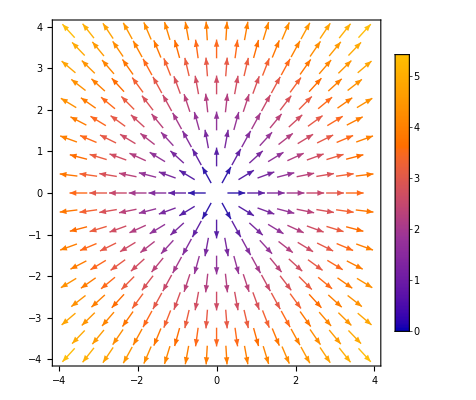

```mathematica
(*divergence of a vector, no curl.*)
VectorPlot[{x,y},{x,-4,4},{y,-4,4},PlotLegends->Automatic]
```

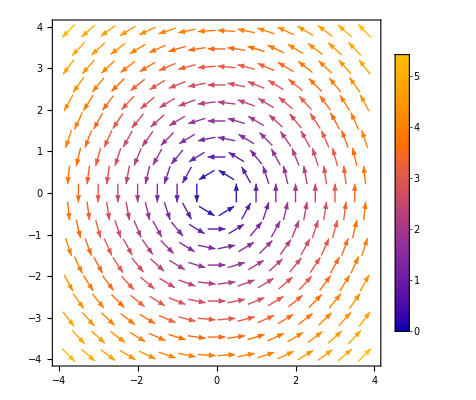

```mathematica
(*curl of a vector, no div.*)
VectorPlot[{-y,x},{x,-4,4},{y,-4,4},PlotLegends->Automatic]
```

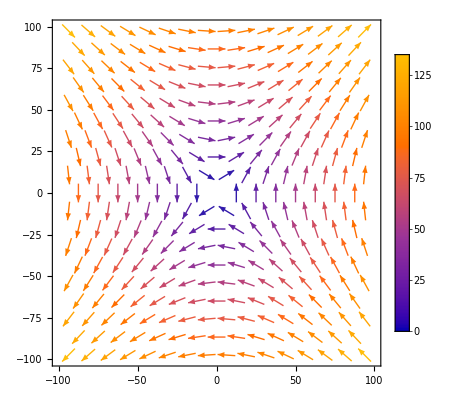

```mathematica
(*no curl, no div.*)
VectorPlot[{y,x},{x,-100,100},{y,-100,100},PlotLegends->Automatic]
(*one of the diagonals is stable, other one is unstable, and the centre is a saddle point.*)
```

stream plot - gives the flow of the vector, does not give the magnitude of the vector.

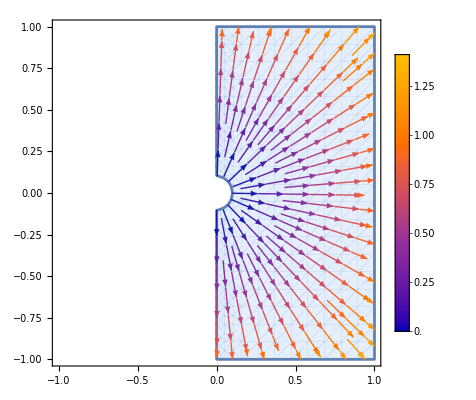

```mathematica
StreamPlot[{x,y},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,vx,vy},x^2+y^2>0.01 && vx>0],PlotLegends->Automatic]
(*
values in the middle would be going haywire, thats why we define region function, it will create a void in the between.
*)
```

```mathematica
StreamPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1},RegionFunction->Function[{x,y,z,vx,vy,vz},x^2+y^2+z^2>0.01 && x>0],PlotLegends->Automatic]
(*
values in the middle would be going haywire, thats why we define region function, it will create a void in the between.
*)
```

-Graphics3D-

```mathematica
VectorPlot3D[{x,y,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScale->0.1,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
VectorPlot3D[{-y,x,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScale->Automatic,PlotLegends->Automatic]
(*
this gives the shape/behaviour of the points in the vector field.
*)
```

-Graphics3D-

```mathematica
Div[{-y,x,z},{x,y,z}]
```

1

```mathematica
Curl[{-y,x,z},{x,y,z}]
```

{0,0,2}

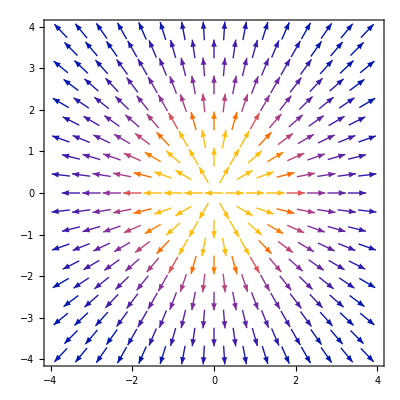

```mathematica
VectorPlot[{x/(x^2+y^2)^1.5,y/((x^2+y^2)^1.5)},{x,-4,4},{y,-4,4}]
```

```mathematica
Div[{x/(x^2+y^2)^1.5,y/((x^2+y^2)^1.5)},{x,y}]
```

-(3. x^2)/((x^2+y^2)^2.5)-(3. y^2)/((x^2+y^2)^2.5)+2/((x^2+y^2)^1.5)

```mathematica
Curl[{x/(x^2+y^2)^1.5,y/((x^2+y^2)^1.5)},{x,y}]
```

0.

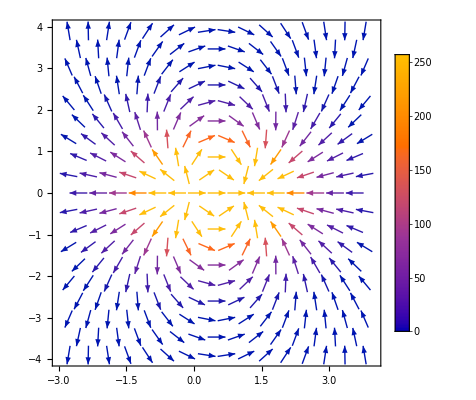

```mathematica
VectorPlot[{(x/(x^2+y^2)^1.5)-((x-1)/((x-1)^2+y^2)^1.5),(y/(x^2+y^2)^1.5)-((y)/((x-1)^2+y^2)^1.5)},{x,-3,4},{y,-4,4},PlotLegends->Automatic]
```

```mathematica
Curl[{(x/(x^2+y^2)^1.5)-((x-1)/((x-1)^2+y^2)^1.5),(y/(x^2+y^2)^1.5)-((y)/((x-1)^2+y^2)^1.5)},{x,y}]
```

0.

```mathematica
Div[{(x/(x^2+y^2)^1.5)-((x-1)/((x-1)^2+y^2)^1.5),(y/(x^2+y^2)^1.5)-((y)/((x-1)^2+y^2)^1.5)},{x,y}]
```

(3. (-1+x)^2)/(((-1+x)^2+y^2)^2.5)+(3. y^2)/(((-1+x)^2+y^2)^2.5)-2/(((-1+x)^2+y^2)^1.5)-(3. x^2)/((x^2+y^2)^2.5)-(3. y^2)/((x^2+y^2)^2.5)+2/((x^2+y^2)^1.5)

```mathematica
Manipulate[VectorPlot[{(c (x/(x^2+y^2)^1.5)-((x-1)/((x-1)^2+y^2)^1.5)),(c1(y/(x^2+y^2)^1.5)-((y)/((x-1)^2+y^2)^1.5))},{x,-3,4},{y,-4,4},PlotLegends->Automatic],{c,-1,1},{c1,-1,1}]
```

```mathematica
Manipulate[VectorPlot[{q1(x/(x^2+y^2)^1.5)+q2((x-10)/((x-10)^2+y^2)^1.5)+ q3 (x+10)/((x+10)^2+y^2)^1.5,q1(y/(x^2+y^2)^1.5)+ q2((y-10)/((x-10)^2+y^2)^1.5)+ q3 ((y-10)/((x-10)^2+y^2)^1.5)},{x,-3,4},{y,-4,4},PlotLegends->Automatic],{q1,-1,1},{q2,-1,1},{q3,-1,1}]
```